```mathematica
(*ustvarimo funkcijo*)
```

```mathematica
f[t_]:=Sin[t] t^2 E^-t;
```

```mathematica
(*ustvarimo novo funkcijo*)
```

```mathematica
priblizek[a_]:=Module[{razvoj},razvoj=Normal[Series[f[t],{t,2,a}]];
Plot[{f[t],razvoj},{t,0,4},PlotStyle->{Blue,Red},PlotRange->All,PlotLegends->{"funkcija","približek"},AxesLabel->{"t","f(t)"}]]
```

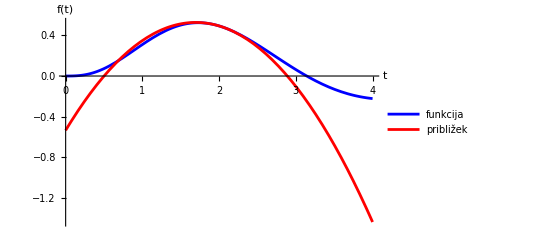

```mathematica
priblizek[2]
```

```mathematica
(*ustarimo še z drsnikom*)
```

```mathematica
Manipulate[priblizek[n],{{n,1,"približek n-tega reda"},1,10,1,Appearance->"Labeled"}]
```